# Understanding Deep Learning Ch 3 Problems

## Define the ReLU activation function

```mathematica
relu[z_]:= If[z < 0, 0, z]
```

```mathematica
a:=relu
```

## Plot a ReLU function

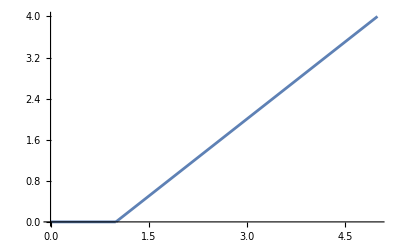

```mathematica
Plot[a[-1+1*x],{x,0,5}]
```

## Define a shallow neural network function

```mathematica
shallowNN[phi0_,phi1_,phi2_,phi3_,
theta10_,theta11_, theta20_,theta21_,theta30_,theta31_,x_]:=
phi0 + phi1*a[theta10+theta11*x]+phi2*a[theta20+theta21*x]+phi3*a[theta30+theta31*x]
```

```mathematica
m1=-100; m2=100;
```

```mathematica
Manipulate[Plot[shallowNN[
phi0,phi1,phi2,phi3,theta10,theta11,theta20,theta21,theta30,theta31,x],{x,0,5}],
 {phi0,m1,m2},{phi1,m1,m2},{phi2,m1,m2},{phi3,m1,m2},
{theta10,m1,m2}, {theta11,m1,m2}, {theta20,m1,m2}, {theta21,m1,m2}, {theta30,m1,m2}, {theta31,m1,m2}]
```

```mathematica
plotSNN[]:=Plot[shallowNN[-0.23,-1.3,1.3,0.66,-0.2,0.4,-0.9,0.9,1.1,-0.7,x],{x,0,5}]
```

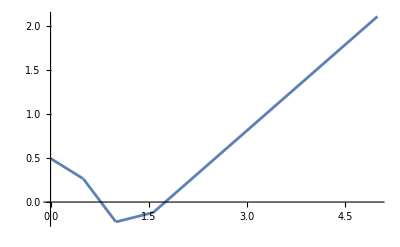

```mathematica
plotSNN[]
```

## Try some other activation functions

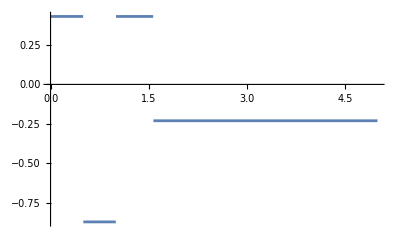

```mathematica
a:=HeavisideTheta
plotSNN[]
```

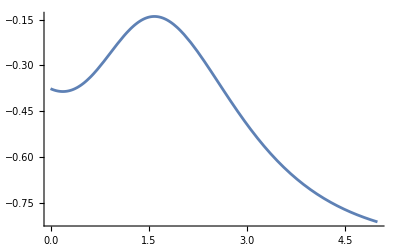

```mathematica
a:=Tanh
plotSNN[]
```

```mathematica
rect[z_]:=If[z>=0&&z<=1,z,0]
```

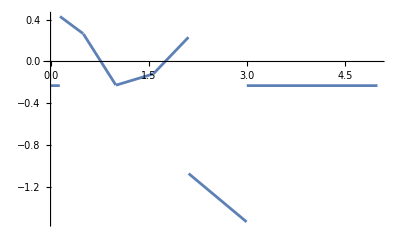

```mathematica
a:=rect
plotSNN[]
```

```mathematica
a:=relu
```